```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
tt=-f0[r,θ]* H[r]+ f2[r,θ]*r^2*Sin[θ]^2W[r,θ]^2;
rr=f1[r,θ]/H[r] ;
θθ=f1[r,θ]*r^2;
ϕϕ=f2[r,θ]* r^2*Sin[θ]^2;
tϕ=-f2[r,θ]*r^2*Sin[θ]^2W[r,θ];
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
f0[r_,t_]:=  1/f2[r,t]
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}];
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}];
christoffel[[2,1,1]]
christoffel[[2,1,1]] /. r-> 4 /. θ -> π/4
christoffel[[2,2,2]]  /. r-> 4 /. θ -> π/4
```

-(H[r] (-f2[r,θ] H'[r]+H[r] f2^(1,0)[r,θ]+r^2 f2[r,θ]^2 Sin[θ]^2 W[r,θ]^2 f2^(1,0)[r,θ]+2 r f2[r,θ]^3 Sin[θ]^2 W[r,θ] (W[r,θ]+r W^(1,0)[r,θ])))/(2 f1[r,θ] f2[r,θ]^2)

-(H[4] (-f2[4,π/4] H'[4]+H[4] f2^(1,0)[4,π/4]+8 f2[4,π/4]^2 W[4,π/4]^2 f2^(1,0)[4,π/4]+4 f2[4,π/4]^3 W[4,π/4] (W[4,π/4]+4 W^(1,0)[4,π/4])))/(2 f1[4,π/4] f2[4,π/4]^2)

1/2 (-H'[4]/H[4]+(f1^(1,0)[4,π/4])/f1[4,π/4])

```mathematica
H[r_]:=1-rh/r;
f1[r_,θ_]:=   (1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2   ;
f2[r_,θ_]:=  1/((1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2)(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);

W[r_,θ_]:=  (1-ct/r)/r^3(√(ct (ct-rh))(rh-2 ct))/(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. 
it calculates whether the trajectory is timelike or null from the variable χ and uinvar which is determined before 
calling the function *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[r[τ]]≤1.01*rh),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
(* This one calculates u dot u *)
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
(* And this one prints out the coordinates *)
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
(* Define various plotting functions *)
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.002} the particle crosses the horizon at τend=69.636

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.0015} the particle crosses the horizon at τend=69.4991

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.001} the particle crosses the horizon at τend=69.5791

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.0005} the particle crosses the horizon at τend=69.8839

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.} the particle crosses the horizon at τend=70.4351

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.0005} the particle crosses the horizon at τend=71.2731

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.001} the particle crosses the horizon at τend=72.4679

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.0015} the particle crosses the horizon at τend=74.1454

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.002} the particle crosses the horizon at τend=76.5553

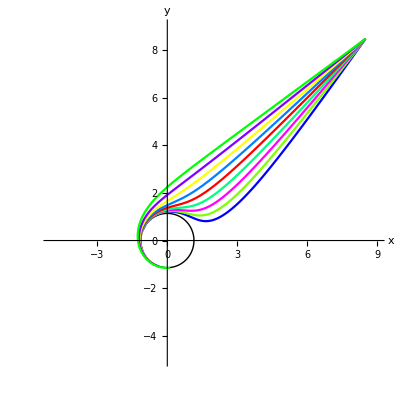

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
horizpl=PolarPlot[rh,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=150;
Table[genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0+i*0.001},1-i*(5/6)],{i,-2,2,0.5}];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-5,9},{-5,9}}]
```

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
ivs={-0.15,0.01,0.017};ics={0,10,π/3,Pi/4};
horizpl=SphericalPlot3D[{rh,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity,PlotPoints->50];
τPlot = 300;
Table[genXYZPlot[τPlot,{0,10,π/3,π/4},{-0.05,0.001,0+i*0.001},1-i*(5/6)],{i,-2,2,1}];
Show[%,horizpl]
```

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,-0.002} the particle crosses the horizon at τend=181.812

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,-0.001} the particle crosses the horizon at τend=174.859

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.} the particle crosses the horizon at τend=177.538

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.001} the particle crosses the horizon at τend=194.52

The particle did not cross the horizon for initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.002}

-Graphics3D-

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.00146} the particle crosses the horizon at τend=73.9888

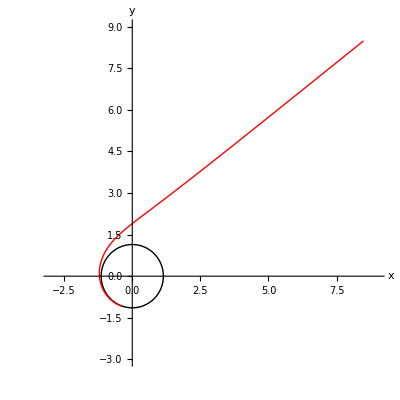

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
horizpl=PolarPlot[rh,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=190;
genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0.00146},1];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-3,9},{-3,9}}]
```

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.0012728} the particle crosses the horizon at τend=73.3116

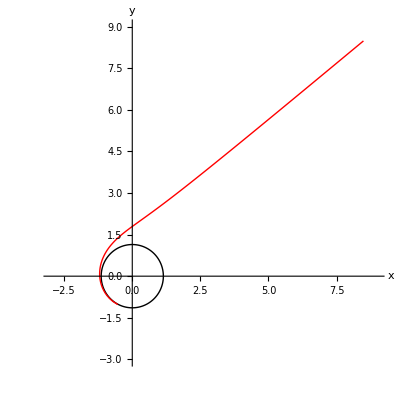

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
horizpl=PolarPlot[rh,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=190;
genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0.0012728},1];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-3,9},{-3,9}}]
```